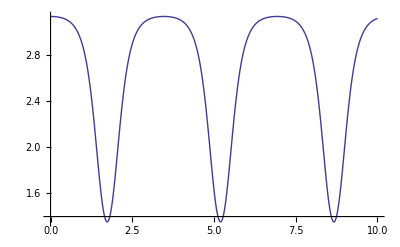

X

(Cos[5 t] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]
Sin[5 t] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]
Cos[InterpolatingFunction[{{0.,10.}},<>][t]])

dX

(-5 Sin[5 t] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]+Cos[5 t] Cos[InterpolatingFunction[{{0.,10.}},<>][t]] InterpolatingFunction[{{0.,10.}},<>][t]
5 Cos[5 t] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]+Cos[InterpolatingFunction[{{0.,10.}},<>][t]] Sin[5 t] InterpolatingFunction[{{0.,10.}},<>][t]
-Sin[InterpolatingFunction[{{0.,10.}},<>][t]] InterpolatingFunction[{{0.,10.}},<>][t])

m

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

T

1/2 (25 (Cos[5 t]^2+Sin[5 t]^2) Sin[InterpolatingFunction[{{0.,10.}},<>][t]]^2+(Cos[InterpolatingFunction[{{0.,10.}},<>][t]]^2 (Cos[5 t]^2+Sin[5 t]^2)+Sin[InterpolatingFunction[{{0.,10.}},<>][t]]^2) (InterpolatingFunction[{{0.,10.}},<>][t])^2)

U

9.81 Cos[InterpolatingFunction[{{0.,10.}},<>][t]]

L

-9.81 Cos[InterpolatingFunction[{{0.,10.}},<>][t]]+1/2 (25 (Cos[5 t]^2+Sin[5 t]^2) Sin[InterpolatingFunction[{{0.,10.}},<>][t]]^2+(Cos[InterpolatingFunction[{{0.,10.}},<>][t]]^2 (Cos[5 t]^2+Sin[5 t]^2)+Sin[InterpolatingFunction[{{0.,10.}},<>][t]]^2) (InterpolatingFunction[{{0.,10.}},<>][t])^2)

dtdq1

InterpolatingFunction[{{0.,10.}},<>][t] (2 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] Sin[InterpolatingFunction[{{0.,10.}},<>][t]] InterpolatingFunction[{{0.,10.}},<>][t]-2 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] (Cos[5 t]^2+Sin[5 t]^2) Sin[InterpolatingFunction[{{0.,10.}},<>][t]] InterpolatingFunction[{{0.,10.}},<>][t])+(Cos[InterpolatingFunction[{{0.,10.}},<>][t]]^2 (Cos[5 t]^2+Sin[5 t]^2)+Sin[InterpolatingFunction[{{0.,10.}},<>][t]]^2) InterpolatingFunction[{{0.,10.}},<>][t]

dq1

9.81 Sin[InterpolatingFunction[{{0.,10.}},<>][t]]+1/2 (50 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] (Cos[5 t]^2+Sin[5 t]^2) Sin[InterpolatingFunction[{{0.,10.}},<>][t]]+(2 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]-2 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] (Cos[5 t]^2+Sin[5 t]^2) Sin[InterpolatingFunction[{{0.,10.}},<>][t]]) (InterpolatingFunction[{{0.,10.}},<>][t])^2)

LangrageDiff

-9.81 Sin[InterpolatingFunction[{{0.,10.}},<>][t]]-25 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]+InterpolatingFunction[{{0.,10.}},<>][t]

```mathematica
Clear["Global`*"];
(* Q - parameters Q = (q1 == alpha) *)
(* Configuration *)
X := R*{
Sin[q1[t]]*Cos[q2[t]], 
Sin[q1[t]]*Sin[q2[t]], 
Cos[q1[t]] }
dX = Simplify[D[X,t]];
m = ({{m1, 0, 0}, {0, m1, 0}, {0, 0, m1}});
(* Trig->False disabled trig. simplifications *)
T = Simplify[(m.dX.dX) / 2, Trig->False];
U = m1*g*(R*Cos[q1[t]]);

(* Lagrange *)
L = T - U;
dtdq1 = D[D[L,q1'[t]],t];
dq1 = D[L,q1[t]];

LangrageDiff = Simplify[dtdq1 - dq1];

(* Example *)

m1 = 1;
R = 1;
g = 9.81;
w = 5;
q2[t_] := w*t;

(*
q1=First[q1/.NDSolve[{LangrageDiff==0,q1[0]==0,q1'[0]==5},q1,{t,0,10}]]
*)
q1 = First[q1 /. NDSolve[{LangrageDiff == 0, q1[0] ==3.13, q1'[0] == 0},q1, {t,0,10}]];
Plot[{q1[t]},{t,0,10}]
Animate[Graphics3D[{Line[{{-1.5,0,0},{1.5,0,0}}],Line[{{0,-1.5,0},{0,1.5,0}}],Line[{{0,0,-1.5},{0,0,1.5}}],
Arrow[{{0,0,0},{
R*Sin[q1[t]]*Cos[0],
R*Sin[q1[t]]*Sin[0],
R*Cos[q1[t]]}}]}],
{t,0,10, 0.001},AnimationRunning->False]

(* Prints *)

Print["X"]
MatrixForm[X]

Print["dX"]
MatrixForm[dX]

Print["m"]
MatrixForm[m]

Print["T"]
MatrixForm[T]

Print["U"]
MatrixForm[U]

Print["L"]
MatrixForm[L]

Print["dtdq1"]
MatrixForm[dtdq1]

Print["dq1"]
MatrixForm[dq1]

Print["LangrageDiff"]
MatrixForm[LangrageDiff]
```

```mathematica
-m1 R (g Sin[q1[t]]+R Cos[q1[t]] Sin[q1[t]] q2'[t]^2-R q1''[t])
```

-9.81 Sin[InterpolatingFunction[{{0.,10.}},<>][t]]-25 Cos[InterpolatingFunction[{{0.,10.}},<>][t]] Sin[InterpolatingFunction[{{0.,10.}},<>][t]]+InterpolatingFunction[{{0.,10.}},<>][t]